## CDW by Electron-Phonon Interaction in ZrTe5

```mathematica
ClearAll["Global`*"]
(*All constants and model parameters*)
{ℏ,ϵ0,e}={1.05 10^-34,8.85 10^-12,1.6 10^-19};
{g0,n0,ϵr}={537.3 10^9 e,8.87 10^(16+6),25.3};
{M0,Mp}={-4.7 ,150 10^-18 }10^-3 e;
Mz=0.01Mp;
{vx,vy,vz}={9,1.9,0.3}10^5; (*Fermi velocities*)
a=8 7.25 10^-10; (*Latticce constant in the direction along magnetic field*)
bz=(2π)/a;
```

### Zeroth Landau Band

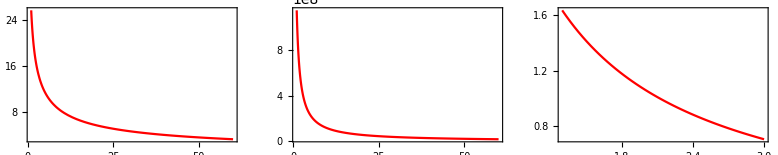

```mathematica
magL[B_]=√(ℏ/(e B)); (*Magnetic Length*)
kF[B_]=2 π^2 n0 magL[B]^2; (*Fermi wave vector*)

(*===Plot to Check===*)
figlB=Plot[10^9 magL[B],{B,1,60},PlotStyle->Red,Frame->True,PlotRange->{All,All}];
figkF=Plot[kF[B],{B,1,60},PlotStyle->Red,Frame->True,PlotRange->All];
figRelakF=Plot[2 kF[B]/bz,{B,1.3,3},PlotStyle->Red,Frame->True,PlotRange->All];
GraphicsRow[{figlB,figkF,figRelakF}]
```

Fermi Level is: 13.0942 meV

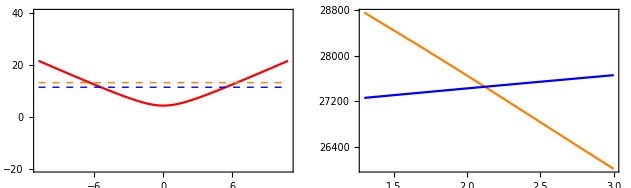

```mathematica
Ek0[k_,B_]=√((ℏ vz  k)^2+(M0+Mp/magL[B]^2+Mz k^2)^2); (* The effective dispersion relation of zeroth Landau (conductance) band in quantum limit*)
vF[B_]=1/ℏ(D[Ek0[k,B], k])/.{k->kF[B]}; (*InCommensurate case*)
vFComm[B_]=1/ℏ(D[Ek0[k,B], k])/.{k->bz/2}; (*8a-Commensurate case*)

(*===Plot to Check===*)
B0=1.8; (*A test strength of magnetic field*)
EF0=Ek0[kF[B0],B0];
EFComm0=Ek0[bz/2,B0];
Print["Fermi Level is: ",10^3 EF0/e," meV"]
figEk=Plot[10^3 Ek0[k,B0]/e,{k,-bz,bz},PlotRange->{{-bz,bz},{-20,40}},PlotStyle-> Red,Frame->True];
figEF=Plot[10^3 EF0/e,{x,-bz,bz},PlotStyle-> {Orange,Dashed,Thick}];
figEFComm=Plot[10^3 EFComm0/e,{x,-bz,bz},PlotStyle-> {Blue,Dashed,Thick}];
figvF=Plot[vF[B],{B,1.3,3},PlotStyle->Orange,Frame->True];
figvFComm=Plot[vFComm[B],{B,1.3,3},PlotStyle->Blue,Frame->True];
GraphicsRow[{Show[figEk,figEF,figEFComm],Show[figvF,figvFComm]}]
```

### Gap

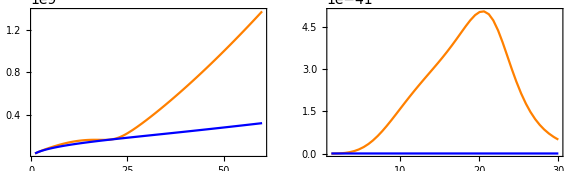

```mathematica
κ[B_]=√((e^3 B)/(4 π^2(ϵ0 ϵr)ℏ^2 vF[B]));  (*dielectric constant from RPA*)

gkF[B_]=g0/(((2kF[B])^2+κ[B]^2)^2);  (**)
gap[B_]=Abs[(ℏ vF[B]kF[B])Csch[(4 π^2 ℏ vF[B] magL[B]^2)/gkF[B]]];
(*===*)
κComm[B_]=√((e^3 B)/(4 π^2(ϵ0 ϵr)ℏ^2 vFComm[B]));

gkFComm[B_]=g0/(((2bz/2)^2+κComm[B]^2)^2);
gapComm[B_]=Abs[(ℏ vFComm[B]bz/2)Csch[(4 π^2 ℏ vFComm[B] magL[B]^2)/gkFComm[B]]];
(*===*)
gkFee[B_]=e^2/(2ϵ0 ϵr((2kF[B])^2+κ[B]^2));
gapee[B_]=Abs[(ℏ vF[B]kF[B])Csch[(4 π^2 ℏ vF[B] magL[B]^2)/gkFee[B]]];


(*===Plot to Check===*)
figκ=Plot[κ[B],{B,1,60},PlotRange->All,PlotStyle->Orange,Frame-> True];
figκComm=Plot[κComm[B],{B,1,60},PlotRange->All,PlotStyle->Blue,Frame-> True];
figgkF=Plot[gkF[B],{B,1.3,30},PlotRange->All,PlotStyle->Orange,Frame-> True];
figgkFComm=Plot[gkFComm[B],{B,1.3,30},PlotRange->All,PlotStyle->Blue,Frame-> True];
GraphicsRow[{Show[figκ,figκComm],Show[figgkF,figgkFComm]}]
```

General::munfl: Csch[5.0069×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Csch[7323.93] is too small to represent as a normalized machine number; precision may be lost.

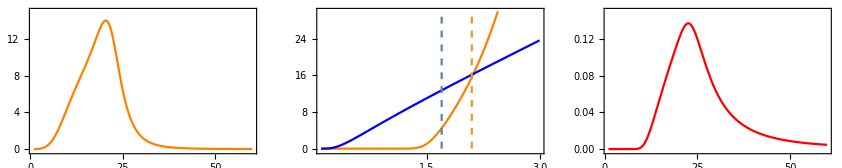

```mathematica
(*===Plot to Show Result===*)
figGap1=Plot[gap[B]/e,{B,1,60},PlotRange->{{1,60},{-0.2,15}},PlotStyle->Orange,Frame-> True];
figGap2=Plot[10^3 gap[B]/e,{B,0.1,3},PlotRange->{{0.1,3},{-0.5,30}},PlotStyle->Orange,Frame-> True];
figGapComm=Plot[10^3 gapComm[B]/e,{B,0.1,3},PlotRange->{{0.1,3},{-0.5,30}},PlotStyle->Blue,Frame-> True];
figGapee=Plot[10^3 gapee[B]/e,{B,1,60},PlotRange->{{1,60},{-0.002,0.15}},PlotStyle->Red,Frame-> True];
Line=ParametricPlot[{{1.7,t},{2.1,t}},{t,0,30},PlotStyle-> {Dashed}];
GraphicsRow[{figGap1,Show[figGap2,figGapComm,Line],figGapee}]
```

### Ground Energy

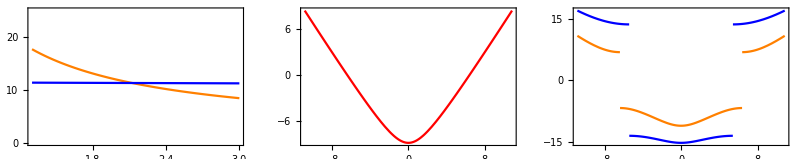

```mathematica
numKz=500;(*per first BZ*)  Lz=numKz a;
dKz=bz/numKz;
EF[B_]=Ek0[kF[B],B];
Ekm[kz_,B_]=Ek0[kz,B]-EF[B];
Egk[kz_,B_]=Piecewise[{{√(Ekm[kz,B]^2+gap[B]^2),kz<-kF[B]},{-√(Ekm[kz,B]^2+gap[B]^2),-kF[B]≤ kz≤ kF[B]},{√(Ekm[kz,B]^2+gap[B]^2),kz>kF[B]}}];
(*===*)
EFComm[B_]=Ek0[bz/2,B];
EkmComm[kz_,B_]=Ek0[kz,B]-EFComm[B];
delEF[B_]=(EFComm[B]-EF[B])*0;
EgkComm[kz_,B_]=Piecewise[{{√(EkmComm[kz,B]^2+gapComm[B]^2)+delEF[B],kz<-bz/2},{-√(EkmComm[kz,B]^2+gapComm[B]^2)+delEF[B],-bz/2≤ kz≤ bz/2},{√(EkmComm[kz,B]^2+gapComm[B]^2)+delEF[B],kz>bz/2}}];
(*===Check===*)
B0=1.8;
figEF=Plot[10^3 EF[B]/e,{B,1.3,3},PlotRange->{All,{0,25}},PlotStyle->Orange,Frame-> True];
figEFComm=Plot[10^3 EFComm[B]/e,{B,1.3,3},PlotRange->{All,{0,25}},PlotStyle->Blue,Frame-> True];
figEkm=Plot[10^3 Ekm[kz,B0]/e,{kz,-bz,bz},PlotRange->{{-bz,bz},All},PlotStyle->Red,Frame-> True];
figEgk=Plot[10^3 Egk[kz,B0]/e,{kz,-bz,bz},PlotRange->{{-bz,bz},All},PlotStyle->Orange,Frame-> True];
figEgkComm=Plot[10^3 EgkComm[kz,B0]/e,{kz,-bz,bz},PlotRange->{{-bz,bz},All},PlotStyle->Blue,Frame-> True];
GraphicsRow[{Show[figEF,figEFComm],figEkm,Show[figEgk,figEgkComm]}]
```

Power::infy: Infinite expression 1/(√0) encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 B ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

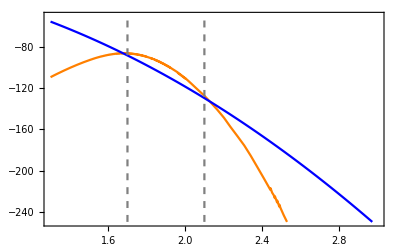

```mathematica
Eg[B_]=1/(2π magL[B]^2 Lz)Sum[(Egk[kz,B]HeavisideTheta[-Egk[kz,B]]),{kz,-bz,bz,dKz}]+gap[B]^2/gkF[B];
EgComm[B_]=1/(2π magL[B]^2 Lz)Sum[(EgkComm[kz,B]HeavisideTheta[-EgkComm[kz,B]]),{kz,-bz,bz,dKz}]+gapComm[B]^2/gkFComm[B];
figEg=Plot[Eg[B],{B,1.3,3},PlotRange->{{1.3,3},{-250,-50}},PlotStyle->Orange,Frame->True];
figEgComm=Plot[EgComm[B],{B,1.3,3},PlotRange->{{1.3,3},{-250,-50}},PlotStyle->Blue,Frame->True];
Line=ParametricPlot[{{1.7,t},{2.1,t}},{t,-250,-50},PlotStyle-> {{Gray,Dashed},{Gray,Dashed}}];
Show[figEg,figEgComm,Line]
```